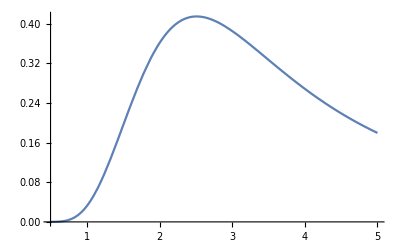

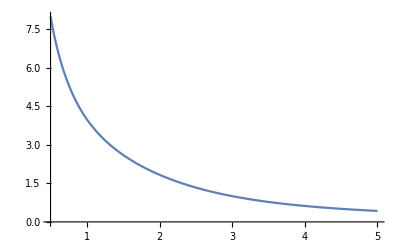

```mathematica
Clear["Global`*"]
Clear[Subscript]
Z=Exp[(8-4h)/T]+4Exp[-2h/T]+4Exp[0/T]+2Exp[-8/T]+4Exp[2h/T]+Exp[(8+4h)/T];
A=-T Log[Z];
Cvmol=-T D[A,{T,2}]/4/.h->0;
totSpin=T D[Log[Z],h];
chimol= D[totSpin,h]/4/.h->0;
Plot[Cvmol,{T,0.5,5}]
Plot[chimol,{T,0.5,5}]
```

```mathematica
Table[Cvmol, {T,0.5,5,0.1}]
Table[chimol, {T,0.5,5,0.1}]
```

{0.0000432135,0.000431885,0.00213136,0.00680649,0.0163197,0.0320823,0.0546476,0.083632,0.117872,0.15569,0.195179,0.234457,0.271847,0.305999,0.335946,0.361096,0.381203,0.396304,0.406649,0.412638,0.414759,0.413539,0.40951,0.403179,0.395012,0.385426,0.374787,0.363406,0.351544,0.339417,0.3272,0.315033,0.303024,0.291259,0.2798,0.268693,0.257967,0.247644,0.237733,0.228239,0.219159,0.210486,0.202212,0.194325,0.18681,0.179655}

{8.,6.66661,5.71397,4.99887,4.44138,3.9933,3.62379,3.31228,3.04462,2.81091,2.60405,2.41894,2.25186,2.10006,1.96144,1.83442,1.71775,1.61039,1.51149,1.42031,1.3362,1.25858,1.18692,1.12072,1.05955,1.00299,0.950652,0.90219,0.85728,0.815624,0.77695,0.741008,0.707571,0.676429,0.647394,0.620291,0.594963,0.571266,0.54907,0.528256,0.508714,0.490347,0.473064,0.456783,0.44143,0.426935}